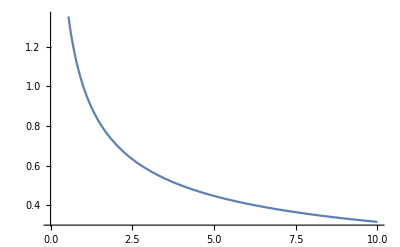

```mathematica
Plot[1/√x,{x,0,10}]
```

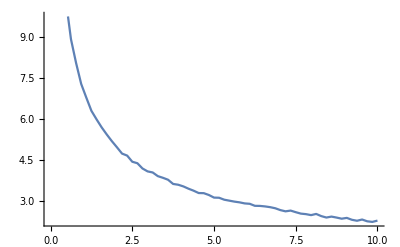

{1.43004,1.22839,1.06655,0.967982,0.902173,0.779799,0.731783,0.749413,0.712566,0.632163,0.632394,0.630435,0.574897,0.54699,0.534832,0.525384,0.511235,0.495016,0.53565,0.519078,0.464839,0.48544,0.452471,0.450048,0.40209,0.475282,0.411349,0.363223,0.387921,0.380038,0.404706,0.403242,0.390267,0.365779,0.359627,0.374718,0.337087,0.328373,0.359693,0.305803,0.361901,0.29358,0.339174,0.352337,0.377149,0.341877,0.284615,0.340232}

```mathematica
f[x_]:=1/√x+RandomReal[{-0.05,0.05}]
Plot[f[0x],{x,0,10},PlotPoints->2]
```

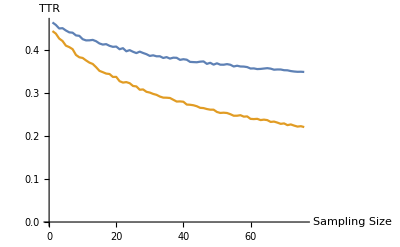

```mathematica
f[x_,y_]:=1/(y √x)+RandomReal[{-0.02,0.02}]/√x
ListPlot[{Table[(f[0.02(x-30),1]+3.4)*0.07,{x,35,50,0.2}],Table[(f[0.02(x-30),0.5])*0.07,{x,35,50,0.2}]},Joined->True,AxesLabel->{"Sampling Size","TTR"}]
```

```mathematica
Export["a.xlsx",{Table[(f[0.02(x-30),1]+3.4)*0.07,{x,35,50,0.2}],Table[(f[0.02(x-30),0.5])*0.07,{x,35,50,0.2}]}]
```

a.xlsx

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["a.xlsx"]]]
```

```mathematica
Table[x,{x,35,50,0.2}]
```

{35.,35.2,35.4,35.6,35.8,36.,36.2,36.4,36.6,36.8,37.,37.2,37.4,37.6,37.8,38.,38.2,38.4,38.6,38.8,39.,39.2,39.4,39.6,39.8,40.,40.2,40.4,40.6,40.8,41.,41.2,41.4,41.6,41.8,42.,42.2,42.4,42.6,42.8,43.,43.2,43.4,43.6,43.8,44.,44.2,44.4,44.6,44.8,45.,45.2,45.4,45.6,45.8,46.,46.2,46.4,46.6,46.8,47.,47.2,47.4,47.6,47.8,48.,48.2,48.4,48.6,48.8,49.,49.2,49.4,49.6,49.8,50.}